# Uniswap V3 Pricing Review for Lenders

## Motivation

With the creation of Uniswap, thorough stochastic pricing analysis has been reviewed by Bardoscia and Milionis describing it’s spot pricing dynamics. Since it’s release, only a few protocols have been created to address leveraged perpetual options using Uniswap V3 pricing dynamics, effectively creating a “loan” based on backed collateral for position holders. Below is a review of simulation using Mathematica to generate empirical risk profiles for V3 positions with standard techniques in Stochastic Calculus. If users are to appropriately price loans for Uniswap V3 positions, simulating worst case lower bounds on losses is important and should be taken into consideration with other methods such as backtesting.

## Stochastic Calculus Review

## Ito’s Lemma

Ito' s Lemma allows us to model functions whose variables are random values . For a function F(X,t) where X is a random variable and t is time, Ito’s lemma gives us a way to model a probability density function for the future time t. We call the variables a “process”, and the result of using Ito’s Lemma a new process.

### Single Variable Ito’s Lemma

Below is the main statement for Ito’s Lemma, as well as it’s code.

-Graphics-

```mathematica
SVIto[F_, var_, stocs_] := Sum[ i[[2]] * D[F, var] * ⅆi[[1]], {i, {{t, α}, {W, β}}}] + 
1/2 β^2*D [F, {var, 2}] * ⅆt /. stocs // Simplify;
```

### Multivariable Ito’s Lemma

When modeling over multiple variables including time, we need the Multivariable Ito’s Lemma. The statement is below as well as it’s code.

-Graphics-

```mathematica
MVIto[F_, vars_, stocs_] := 
Sum[ D[F, {var}] * ⅆvar, {var, vars}] + 
Sum[  1/2 D [F, pairs[[1]], pairs[[2]]] * ⅆpairs[[1]] * ⅆpairs[[2]],{pairs, Subsets[vars, {2}] ~Join~ Map[{#, #}&,vars]}]  /. stocs // Simplify;
```

### Sanity Checks

Below are some sanity checks for known processes.

#### Geometric Brownian Motion

Geometric Brownian Motion is a process that assumes random percent changes . Rather than random step changes, this has features where the value is not negative and is modeled in lots of natural processes.

```mathematica
diffGBM =ⅆS -> S (μ + σ^2/2) ⅆt + S σ ⅆW;
```

```mathematica
SVIto @@ {ⅇ^S, S, {ⅆS -> μ  ⅆt + σ  ⅆW, α -> μ , β -> σ} }  // (#/ⅇ^S)& // Simplify
```

(μ+σ^2/2) ⅆt+σ ⅆW

#### Forward Processes

The Multi-variable Ito should correctly return the Forward Contract process.

```mathematica
MVIto@@{ S*ⅇ^(y(T-t)), {S, t},{ⅆS -> μ S ⅆt + σ S ⅆW} }
```

1/2 ⅇ^((-t+T) y) S (-2+y ⅆt) ((y-μ) ⅆt-σ ⅆW)

#### Log-Normal Processes

The Multi-variable Ito should correctly return the Log Normal process.

```mathematica
MVIto@@{ Log[S], {S, t}, {ⅆS -> μ S ⅆt + σ S ⅆW}} //
Expand //
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0} ) &// 
Simplify
```

(μ-σ^2/2) ⅆt+σ ⅆW

#### Ornstien-Uhlenbeck

Ornstien-Uhlenbeck processes drive to the mean μ as time goes on. This is in effect a mean reverting process model.

```mathematica
diffOrnstienUhlenbeck = ⅆX -> κ  (μ -X) ⅆt + σⅆW;
```

```mathematica
SVIto[X^2, X, {α-> -κ * X, β -> σ}]
```

(-2 X^2 κ+σ^2) ⅆt+2 X σ ⅆW

```mathematica
MVIto[X^2, {X,t}, {ⅆX -> - κ * X ⅆt + σⅆW }] //
Expand // 
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0})& //
Simplify
```

(-2 X^2 κ+σ^2) ⅆt+2 X σ ⅆW

## Uniswap V3 Stochastic Analysis

Now that we have Ito’s Lemma defined, we can use the program to determine some average case and variances for Uniswap’s value functions.

## Uniswap State Equations

Below, are some necessary equations for Uniswap V3 analysis. In these equations, treat Y as a cash-like stable numeraire. Prices are in terms of the numeraire per X token (USD per ETH). p_a represents the lower bound of the position, and p_b is the upper bound.

```mathematica
liquidityEquation = (x + L/(√Subscript[p, b]))(y + L √Subscript[p, a]) == L^2;
tokensGivenLiquidity = { x -> L (√Subscript[p, b]-√p)/(√p * √Subscript[p, b]), y -> L (√p - √Subscript[p, a])};
liquidityGivenTokens = { Subscript[L, x] ->x *(√p * √Subscript[p, b])/(√Subscript[p, b] -√p) , Subscript[L, y] -> y/(√p - √Subscript[p, a])};
```

```mathematica
Liquidity[lowerPriceBound_, upperPriceBound_, currentPrice_, total_] :=
 Solve[
(Subscript[L, x] == Subscript[L, y] /. liquidityGivenTokens /.{x -> holdX , y -> holdY , p -> currentPrice , Subscript[p, a] -> lowerPriceBound, Subscript[p, b] -> upperPriceBound}) &&
holdX >0 && holdY > 0 && total == holdX*currentPrice + holdY, {holdX, holdY}] // ({ x -> holdX, y -> holdY, L -> holdY/(√currentPrice- √lowerPriceBound) } /. #)&;
```

```mathematica
Liquidity[1600, 1700, 1628, 10000] // N
1628*x + y  /. %
```

{{x→4.37661,y→2874.87,L→8249.71}}

{10000.}

```mathematica
originalValue = x*p + y /. tokensGivenLiquidity /. {Subscript[p, a] -> lower, Subscript[p, b] -> higher, p -> startPrice };
currentValue = x*p + y /. tokensGivenLiquidity /.  {Subscript[p, a] -> lower, Subscript[p, b] -> higher};
IL =(currentValue - originalValue)/originalValue;
humanReadable = { lower -> Subscript[p, a], higher -> Subscript[p, b] , startPrice -> Subscript[p, 0]};
IL /. humanReadable // Simplify;
```

## Pricing Derivations for Impermanent Loss

Taking a look at a particular example, we can derive some interesting results with the Uniswap math. Below is a close enough situation to reality using the curves. The block directly below is just a setup

```mathematica
ethDailyVol = 0.0034;
ethMeanYearly = 0.1;
currentPrice = 1628;
lowerBound = 1600;
upperBound = 1700;
initialValue = 10000;
currentLiquidityParams =Liquidity[lowerBound, upperBound, currentPrice, initialValue] // N
```

{{x→4.37661,y→2874.87,L→8249.71}}

### Plotting to Understand Value Curves

Let’s load the example into the curves and take a look at them to determine value action across price.

```mathematica
valueCurve =currentValue  /. currentLiquidityParams;
```

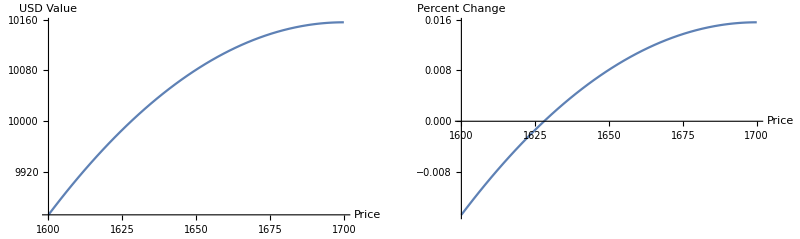

```mathematica
GraphicsGrid[{{
Plot[valueCurve /. { lower -> lowerBound, higher -> upperBound , startPrice -> currentPrice}, {p, lowerBound, upperBound}, AxesLabel->{"Price", "USD Value"}],
Plot[IL /. { lower -> lowerBound, higher -> upperBound , startPrice -> currentPrice}, {p, lowerBound, upperBound},  AxesLabel->{"Price", "Percent Change"}]
}}]
```

#### Closed Form Analysis

Because Wolfram acts symbolically, we can derive some processes directly and compute means and variances.

```mathematica
procPVOpen = TransformedProcess[currentValue /. {p -> p[t]},p \[Distributed] GeometricBrownianMotionProcess[μ, σ, S],
t];
meanProcPVOpen = Mean[procPVOpen[t]];
varianceProcPVOpen = Variance[procPVOpen[t]];
```

```mathematica
TableForm[{
{"Mean Function", meanProcPVOpen /. {higher -> Subscript[p, b], lower -> Subscript[p, a]}},
{"Variance", varianceProcPVOpen/. {higher -> Subscript[p, b], lower -> Subscript[p, a]}}
}]
```

Mean Function | L (2 ⅇ^(1/8 t (4 μ-σ^2)) √S-√p_a-(ⅇ^(t μ) S)/(√p_b))
Variance | (ⅇ^(t (μ-σ^2/4)) (-1+ⅇ^((t σ^2)/4)) L^2 S ((ⅇ^(t (μ+(3 σ^2)/4))+ⅇ^(t (μ+σ^2))+ⅇ^(1/4 t (4 μ+σ^2))+ⅇ^(t μ+(t σ^2)/2)) S-4 ⅇ^(1/8 t (4 μ+σ^2)) (1+ⅇ^((t σ^2)/4)) √S √p_b+4 p_b))/p_b

From this we have a clear closed form solution for the mean and variance, so one can produce 95% confidence intervals.

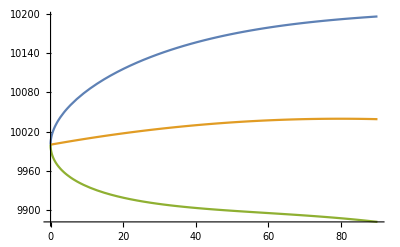

```mathematica
funcsPVOpen = {
meanProcPVOpen +√varianceProcPVOpen,
meanProcPVOpen,
meanProcPVOpen -√varianceProcPVOpen
}/. {higher -> upperBound, lower -> lowerBound, μ -> ethMeanYearly/365, σ -> ethDailyVol, S -> currentPrice } /. currentLiquidityParams[[1]] // Simplify;
boundsPlot =Plot[funcsPVOpen, {t, 0, 90}]
```

```mathematica
ILOpen =MVIto@@{IL, {p, t},{(diffGBM /. {S-> p})} } // 
Expand //
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0} ) &// 
Simplify
procILOpen = ItoProcess[ (ⅆV[t] == IL /. {p -> p[t]}),{V[t]}, {V, Subscript[V, 0]},{t, 0},{ W \[Distributed] WienerProcess[], p \[Distributed] GeometricBrownianMotionProcess[μ, σ, S]}];
TableForm[{
{"Mean Function", Mean[procILOpen[t]] /. {higher -> Subscript[p, b], lower -> Subscript[p, a], startPrice -> Subscript[p, 0]}},
{"Variance", Variance[procILOpen[t]]/. {higher -> Subscript[p, b], lower -> Subscript[p, a],startPrice -> Subscript[p, 0]}}
}]
```

((2 p (2 μ+σ^2)-√higher √p (4 μ+σ^2)) ⅆt+(-4 √higher √p σ+4 p σ) ⅆW)/(4 (√higher (√lower-2 √startPrice)+startPrice))

Mean Function | V_0
Variance | 0

#### Pricing With IL

```mathematica
resultIL =MVIto@@{IL, {p, t},{(diffGBM /. {S-> p})} } // 
Expand //
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0} ) &// 
Simplify;
resultIL /. humanReadable
```

(ⅆW (4 p σ-4 √p σ √p_b)+ⅆt (2 p (2 μ+σ^2)-√p (4 μ+σ^2) √p_b))/(4 (p_0+(-2 √p_0+√p_a) √p_b))

```mathematica
preprocessIL = resultIL /. currentLiquidityParams[[1]]/. 
{p -> p[t], W -> W[t],lower -> lowerBound, higher -> upperBound ,μ -> ethMeanYearly/365, σ -> ethDailyVol, startPrice -> currentPrice} // N // Simplify
```

0.000228404 ⅆt √p[t]+0.0028049 ⅆW[t] √p[t]-5.59742×10^-6 ⅆt p[t]-0.0000680288 ⅆW[t] p[t]

```mathematica
procIL = ItoProcess[ ⅆV[t] == preprocessIL,V[t], {V,10000}, {t, 0},{ W \[Distributed] WienerProcess[], p \[Distributed] GeometricBrownianMotionProcess[ethMeanYearly/365, ethDailyVol, currentPrice]}];
fsIL = RandomFunction[procIL, {0, 90}, 5];
```

```mathematica
Mean[fsIL[90]]
```

10000.

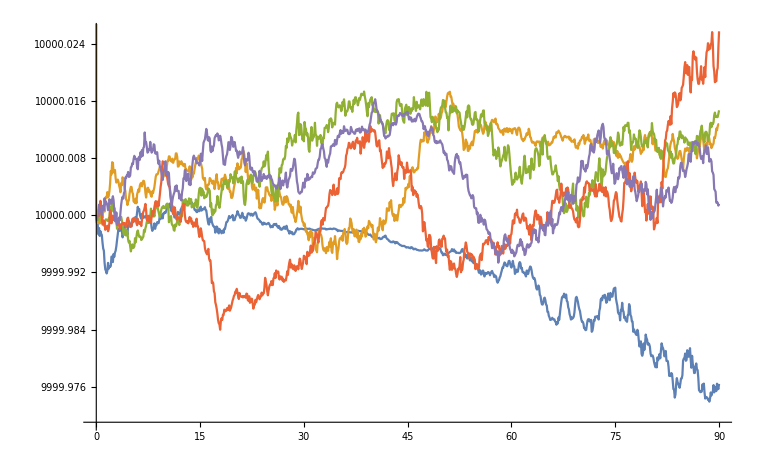

```mathematica
Show[
ListLinePlot[fsIL, FillingStyle->Axis], 
boundsPlot
]
```

#### Pricing with Position Value

```mathematica
preprocessPV = currentValue /. {lower -> lowerBound, higher -> upperBound , p -> p[t]} /. currentLiquidityParams;
```

```mathematica
preprocessPV
```

{8249.71 (-40+√p[t])+200.085 (10 √17-√p[t]) √p[t]}

```mathematica
procPV = TransformedProcess[preprocessPV,{ p \[Distributed] GeometricBrownianMotionProcess[ethMeanYearly/365, ethDailyVol, currentPrice]},
t];
fsPV = RandomFunction[procPV, {0, 90,1}, 5];
```

```mathematica
Mean[fsPV[90]]
```

10012.5

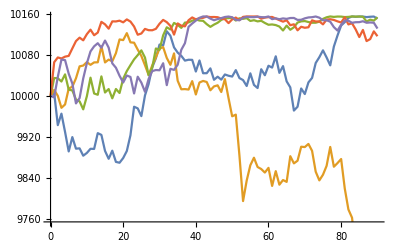

```mathematica
ListLinePlot[fsPV, FillingStyle->Axis]
```

## Further Research

```mathematica
TableForm[{
{"Impermanent Loss in Uniswap V3", Hyperlink["https://lambert-guillaume.medium.com/an-analysis-of-the-expected-value-of-the-impermanent-loss-in-uniswap-bfbfebbefed2"]},
{"Uniswap Liquidity V3 Math", Hyperlink["http://atiselsts.github.io/pdfs/uniswap-v3-liquidity-math.pdf"]}
}]
```

Impermanent Loss in Uniswap V3 | https://lambert-guillaume.medium.com/an-analysis-of-the-expected-value-of-the-impermanent-loss-in-uniswap-bfbfebbefed2
Uniswap Liquidity V3 Math | http://atiselsts.github.io/pdfs/uniswap-v3-liquidity-math.pdf

## Perpetual Lending Stochastic Analysis

## Mean-Reverting Additional Value Term

TBD